Problem 2: Explore making h variable in the kernel density estimator. This means use a different h for each point in the sample.

(a) Choose a scalar random variable X. Generate a random sample from the distribution using small n (n=10 or so). Choose h for each point determined by how close it is to the other points. Compare your KDE (variable h) to the KDE resulting from using fixed h. Compare both KDEs to the PDF of X.

(b) Do the same thing in the bivariate case using the bivariate normal.

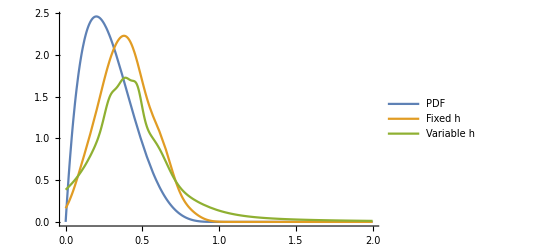

```mathematica
OneD=Sort[RandomVariate[BetaDistribution[3,5],50]];
sig1=0.075;
sig2[k_]=20If[k==1,OneD[[2]]-OneD[[1]],If[k==50,OneD[[50]]-OneD[[49]],(OneD[[k+1]]-OneD[[k-1]])/2]];
p1[x_]=Sum[PDF[NormalDistribution[OneD[[k]],sig1],x],{k,1,50}]/50;
p2[x_]=Sum[PDF[NormalDistribution[OneD[[k]],sig2[k]],x],{k,1,50}]/50;
Plot[{PDF[BetaDistribution[2,5],x],p1[x],p2[x]},{x,0,2},PlotRange->All,PlotLegends->{"PDF","Fixed h","Variable h"}]
```

```mathematica
ThreeD=RandomVariate[MultinormalDistribution[{3,3},{{1,0},{0,2}}],50];
sig=0.1;
maxDist=Sqrt[(Max[ThreeD[[;;,1]]]-Min[ThreeD[[;;,1]]])^2+(Max[ThreeD[[;;,2]]]-Min[ThreeD[[;;,2]]])^2];
distMax=ConstantArray[maxDist,50];
For[i=1,i≤50,i++,
For[j=1,j≤50,j++,
newDist=distMax[[1]];
If[i≠j,newDist=√((ThreeD[[i,1]]-ThreeD[[j,1]])^2+(ThreeD[[i,2]]-ThreeD[[j,2]])^2),Continue];
If[newDist<distMax[[i]],distMax[[i]]=newDist,Continue];]]
p1[x_,y_]=Sum[PDF[MultinormalDistribution[ThreeD[[k]],{{sig,0},{0,sig}}],{x,y}],{k,1,50}]/50;
p2[x_,y_]=Sum[PDF[MultinormalDistribution[ThreeD[[k]],{{distMax[[k]],0},{0,distMax[[k]]}}],{x,y}],{k,1,50}]/50;
Plot3D[{PDF[MultinormalDistribution[{3,3},{{0.5,0},{0,1}}],{x,y}],p1[x,y],p2[x,y]},{x,-1,7},{y,-2,8},PlotRange->All,
AxesLabel->{Style["x",14,Blue],Style["y",14,Blue]},PlotLegends->{"PDF","Fixed h","Variable h"},
PlotLabel->Style["KDEs for Class 1, 2, 3",16,Blue]]
```

-Graphics3D-